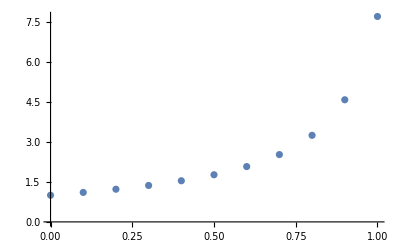

```mathematica
Clear[y]
f[x_,y_]:=y^2-x
y[0]=1;
h:=0.1;
Do[k1=h f[h n,y[n]];
k2=h f[h (n+1),y[n]+k1];
y[n+1]=y[n]+.5 (k1+k2),{n,0,10}]
a=ListPlot[Table[{n*h,y[n]},{n,0,10}]]
```

```mathematica
y[10]
```

7.70586

```mathematica
Clear[y];
```

```mathematica
s=NDSolve[{y'[x]==y[x]^2-x,y[0]==1},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

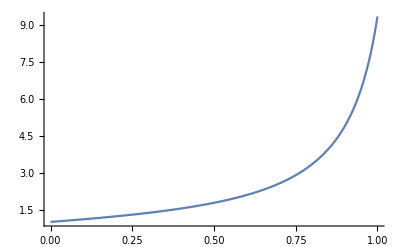

```mathematica
b=Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

```mathematica
y[1]/.s
```

{9.35382}

1

0.05

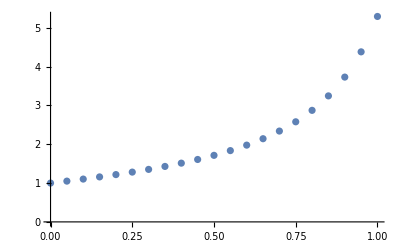

```mathematica
Clear[y]
f[x_,y_]:=y^2-x
y[0]=1
h=.05
Do[y[n]=y[n-1]+h*f[(n-1)*h,y[n-1]],{n,1,20}]
c=ListPlot[Table[{n*h,y[n]},{n,0,20}]]
```

```mathematica
y[20]
```

5.28984

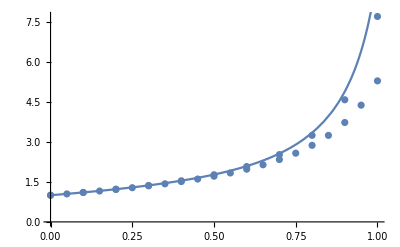

```mathematica
Show[a,b,c]
```

```mathematica
DifferenceImproveEulerAndExact = 9.353820831189541-7.705859706388908
DifferenceEulerandImprovedEuler = 7.705859706388908-5.289844541843895
```

1.64796

2.41602

```mathematica
(Clearly, improved Euler's method is much more accurate)
```

```mathematica
Clear[a,c,y,x];
```

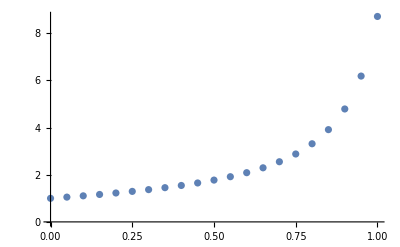

```mathematica
f[x_,y_]:=y^2-x
y[0]=1;
h:=0.05;
Do[k1=h f[h n,y[n]];
k2=h f[h (n+1),y[n]+k1];
y[n+1]=y[n]+.5 (k1+k2),{n,0,20}]
a=ListPlot[Table[{n*h,y[n]},{n,0,20}]]
```

```mathematica
y[20]
```

8.71523

```mathematica
Clear[y];
s=NDSolve[{y'[x]==y[x]^2-x,y[0]==1},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
b=Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
y[1]/.s
```

{9.35382}

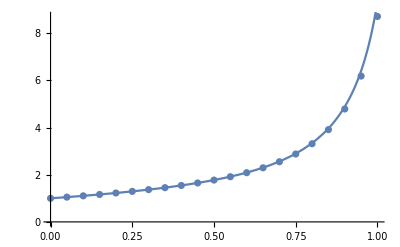

```mathematica
Show[a,b]
```

```mathematica
DifferenceImproveEulerAndExact = 9.353820831189541-8.715234970278456
```

0.638586

```mathematica
(As we can see, as the step size gets smaler, The improved Euler Method becomes far more precise)
```